### Specific to the case of trefoil, for which the following f_n’s are defined

```mathematica
f=<||>;
```

```mathematica
f[1]=1;
f[3]=2;
f[5]=1/q+3+q;
f[7]=2/q^2+2/q+5+2 q+2 q^2;
f[9]=1/q^4+3/q^3+4/q^2+5/q+8+5 q+4 q^2+3 q^3+q^4;
f[11]=2/q^6+2/q^5+6/q^4+7/q^3+10/q^2+10/q+15+10 q+10 q^2+7 q^3+6 q^4+2 q^5+2 q^6;
f[13]=1/q^9+3/q^8+4/q^7+7/q^6+11/q^5+15/q^4+18/q^3+21/q^2+23/q+27+23 q+21 q^2+18 q^3+15 q^4+11 q^5+7 q^6+4 q^7+3 q^8-3 q^8+q^9;
```

```mathematica
Do[f[n+14]=Simplify[-q^(-n/2-11/2)/(q^(n/2+13/2)-1)*(f[n] (q^(n/2+17/2)-q^(n+9))+f[n+2] (q^(n/2+15/2)-q^(n/2+17/2)+q^(n+9)-q^(n+10))+f[n+4] (-q^(n/2+11/2)-q^(n/2+17/2)-q^(n/2+19/2)+q^(3 n/2+21/2)+q^(n+8)+q^(n+9)+q^(n+12))+f[n+6] (-q^(n/2+9/2)+q^(n/2+11/2)-q^(n/2+15/2)-q^(n/2+17/2)+q^(3 n/2+25/2)+q^(n+9)+q^(n+10)-q^(n+12)+q^(n+13))+f[n+8] (q^(n/2+11/2)+q^(n/2+13/2)-q^(n/2+17/2)+q^(n/2+19/2)-q^(3 n/2+31/2)-q^(n+8)-q^(n+9)+q^(n+11)-q^(n+12))+f[n+10] (q^(n/2+9/2)+q^(n/2+11/2)+q^(n/2+17/2)-q^(3 n/2+35/2)-q^(n+9)-q^(n+12)-q^(n+13))+f[n+12] (q^(n/2+11/2)-q^(n/2+13/2)+q^(n+11)-q^(n+12))-f[n+4] q^7-f[n+6] q^5+f[n+8] q^2+f[n+10])];
,{n,1,50,2}]
```

```mathematica
u[r_,m_]:={1/2(1/r+m),1/2(-1/r+m),-1/2(1/r+m),1/2(1/r-m)}
```

```mathematica
xpref[m_,p_,r_,a_]:=Simplify[Sum[(-1)^(n-1)(Boole[IntegerQ[(r u[r,m][[n]]-a)/p]]q^(-u[r,m][[n]]^2 r/p)),{n,1,4}]]
```

```mathematica
pf[p_,r_,a_,trunc_]:=Series[Sum[xpref[m,p,r,a]f[m],{m,1,30,2}],{q,0,trunc}]
```

```mathematica
-pf[-1,2,0,30]/q^(4/5)/2
```

0

```mathematica
pf3[p_,r_,a_,trunc_]:=Series[Sum[xpref[m,p,r,a]f3[m],{m,1,50,2}],{q,0,trunc}]
```

```mathematica
f3[m_]:=q^((m^2-1)/24)
```

### Trefoil p=-1, a=0, various r

```mathematica
-pf3[-1,1,0,50]/2
```

1-q+q^(4/3)-q^(13/3)+q^5-q^10+q^11-q^18+q^(58/3)-q^(85/3)+q^30-q^41+q^43+O[q]^(151/3)

### Try p=-1, r=2, a=0

```mathematica
-pf[-1,2,1/2,30]/q^(1/8)/2
```

1-q+2 q^3-2 q^6+q^9+3 q^10+q^11-q^14-3 q^15-q^16+2 q^19+2 q^20+5 q^21+2 q^22+2 q^23-2 q^26-2 q^27-5 q^28-2 q^29+O[q]^30

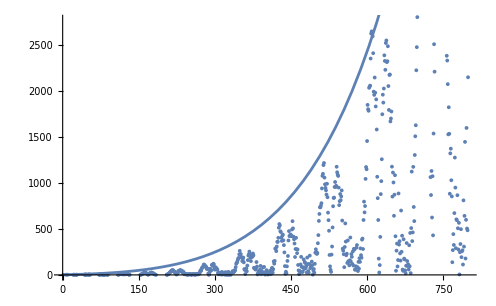

```mathematica
trunc=800;
data4=-pf[-1,4,1/2,trunc]/2/q^(9/16);
list4=Exponent[data4,q,List];
(*ListPlot[Table[list4[[i+1]]-list4[[i]],{i,1,Length[list4]-1}]]*)
coef4=Table[Coefficient[data4,q^(list4[[n]])],{n,2,Length[list4]}];
coef4p=Table[Abs[Coefficient[data4,q^(list4[[n]])]],{n,2,Length[list4]}];
Show[ListPlot[Transpose[{Rest[list4],coef4p}]],Plot[E^(2/(2 Pi)Sqrt[x]),{x,0,trunc}]]
```

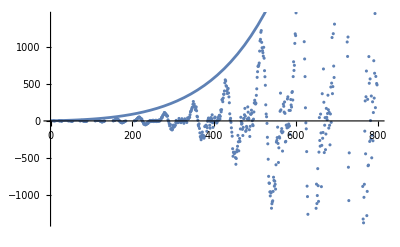

```mathematica
Show[ListPlot[Transpose[{Rest[list4],coef4}]],Plot[E^(2/(2 Pi)Sqrt[x]),{x,0,trunc}]]
```

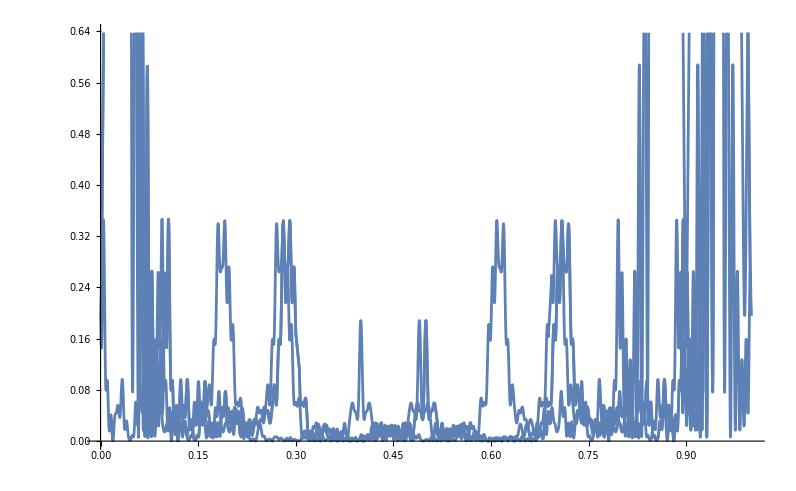

```mathematica
β={0,0.01,0.1,1};
Plot[Table[Norm[(z3/.q->E^(2 I Pi (t+β[[i]])))]^2/52039,{i,1,4}],{t,0,1}]
```

```mathematica
Plot[z3^2,{t,0,4}]
```

-Graphics-

```mathematica
list3=Exponent[%,q,List]
```

{0}

```mathematica
ListPlot[Table[Log[(list3[[i+1]]-list3[[i]])/(list3[[i]]-list3[[i-1]])],{i,2,Length[list3]-1}]]
```

-Graphics-

```mathematica
ListPlot[Table[list3[[i+1]]-list3[[i]],{i,1,Length[list3]-1}]]
```

-Graphics-

it seems like (r u - a)/p∈ℤ is never true where u = {1/2 (1/2+m),1/2 (-(1/2)+m), -1/2 (1/2+m),1/2 (1/2-m)}

```mathematica
uu = {1/2(1/r+m),1/2(-1/r+m),-1/2(1/r+m),1/2(1/r-m)};
```

```mathematica
Table[uu/.{r->2},{m,1,50}]
```

{{3/4,1/4,-3/4,-1/4},{5/4,3/4,-5/4,-3/4},{7/4,5/4,-7/4,-5/4},{9/4,7/4,-9/4,-7/4},{11/4,9/4,-11/4,-9/4},{13/4,11/4,-13/4,-11/4},{15/4,13/4,-15/4,-13/4},{17/4,15/4,-17/4,-15/4},{19/4,17/4,-19/4,-17/4},{21/4,19/4,-21/4,-19/4},{23/4,21/4,-23/4,-21/4},{25/4,23/4,-25/4,-23/4},{27/4,25/4,-27/4,-25/4},{29/4,27/4,-29/4,-27/4},{31/4,29/4,-31/4,-29/4},{33/4,31/4,-33/4,-31/4},{35/4,33/4,-35/4,-33/4},{37/4,35/4,-37/4,-35/4},{39/4,37/4,-39/4,-37/4},{41/4,39/4,-41/4,-39/4},{43/4,41/4,-43/4,-41/4},{45/4,43/4,-45/4,-43/4},{47/4,45/4,-47/4,-45/4},{49/4,47/4,-49/4,-47/4},{51/4,49/4,-51/4,-49/4},{53/4,51/4,-53/4,-51/4},{55/4,53/4,-55/4,-53/4},{57/4,55/4,-57/4,-55/4},{59/4,57/4,-59/4,-57/4},{61/4,59/4,-61/4,-59/4},{63/4,61/4,-63/4,-61/4},{65/4,63/4,-65/4,-63/4},{67/4,65/4,-67/4,-65/4},{69/4,67/4,-69/4,-67/4},{71/4,69/4,-71/4,-69/4},{73/4,71/4,-73/4,-71/4},{75/4,73/4,-75/4,-73/4},{77/4,75/4,-77/4,-75/4},{79/4,77/4,-79/4,-77/4},{81/4,79/4,-81/4,-79/4},{83/4,81/4,-83/4,-81/4},{85/4,83/4,-85/4,-83/4},{87/4,85/4,-87/4,-85/4},{89/4,87/4,-89/4,-87/4},{91/4,89/4,-91/4,-89/4},{93/4,91/4,-93/4,-91/4},{95/4,93/4,-95/4,-93/4},{97/4,95/4,-97/4,-95/4},{99/4,97/4,-99/4,-97/4},{101/4,99/4,-101/4,-99/4}}

When i turn p = -1/2, the result does look like something, however not found as any series in the paper

```mathematica
-pf[-1/2,2,0,40]q^(-1/4)/2
```

1-q^2+2 q^6-2 q^12+q^19+3 q^20+q^21-q^29-3 q^30-q^31+O[q]^40

```mathematica
Keys[f]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63}